Homework-4
Youssef Tawfik
201800418

## Diffusion of a GaAs/Al_x Ga_(1-x)As Junction

```mathematica
ClearAll["Global`*"]

dz=1.;dt=0.01;tf=100.;
z=Range[0.,400.,dz];lz=Length[z];
x=xp=0.*z;
If[Mod[lz,2]==0,i0=lz/2,i0=(lz+1)/2];
x0=0.1;diff=10.;
xp⟦Range[i0]⟧=ConstantArray[x0,i0];
tplots={0.,10.,50.,tf};
xplots=0.*tplots;

n=1;Do[
If[t==tplots⟦n⟧,xplots⟦n⟧=xp;n++];
Do[
x⟦j⟧=xp⟦j⟧+dt*diff*1/dz^2(xp⟦j+1⟧-2xp⟦j⟧+xp⟦j-1⟧);
,{j,2,lz-1}];
x⟦{1,-1}⟧=x⟦{2,-2}⟧;
xp=x;
,{t,0.,tf,dt}];
```

## Plot Generation

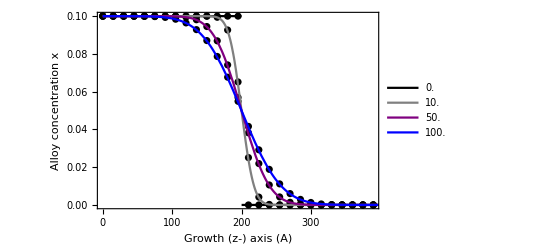

```mathematica
color={ Black,Gray, Purple, Blue, Red};
plots=nplots=0*tplots;
Do[plots⟦i⟧=Plot[x0/2 Erfc[(z-200)/(2 √(diff*tplots⟦i⟧))],{z,0,400.},PlotStyle->color⟦i⟧]
,{i,2,Length[tplots]}];
plots⟦1⟧=Plot[0.1*UnitStep[-z+200],{z,0.,400.},PlotStyle-> color⟦1⟧];
Do[nplots⟦k⟧=ListPlot[Table[{z⟦i⟧,xplots⟦k,i⟧},{i,1,lz,15}],PlotStyle-> Black]
,{k,1,Length[tplots]}];


Legended[Show[
nplots,plots,
Frame-> True,FrameLabel-> {"Growth (z-) axis (A)","Alloy concentration x"}],
LineLegend[color,tplots]]
```

## Diffusion in a Quantum Well

```mathematica
ClearAll["Global`*"]

dz=1;dt=0.01;tf=1000.;
well=200.;border=200.;
lw=Floor[well/dz];lb=Floor[well/dz];
z=Range[0.,2*border+well,dz];lz=Length[z];
x=xp=0.*z;
x0=0.1;diff=10;
xp⟦Range[lb]⟧=xp⟦-Range[lb]⟧=ConstantArray[x0,lb];
tplots={10.,20.,50.,100.,200.,500.,1000.};
xplots=0.*tplots;
n=1;

Do[
Do[
x⟦j⟧=xp⟦j⟧+dt*diff*1/dz^2(xp⟦j+1⟧-2xp⟦j⟧+xp⟦j-1⟧);
,{j,2,lz-1}];
x⟦{1,-1}⟧=x⟦{2,-2}⟧;
xp=x;

If[t==tplots⟦n⟧,xplots⟦n⟧=x;n++]
,{t,dt,tf,dt}];
```

## Plot Generation

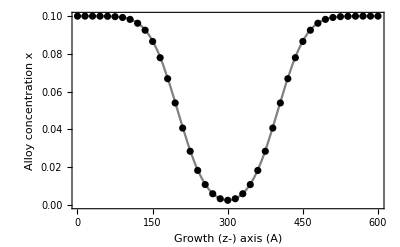

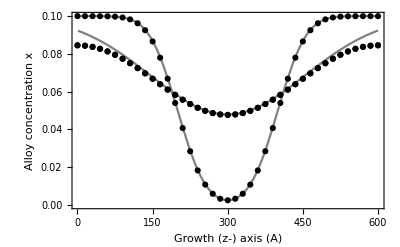

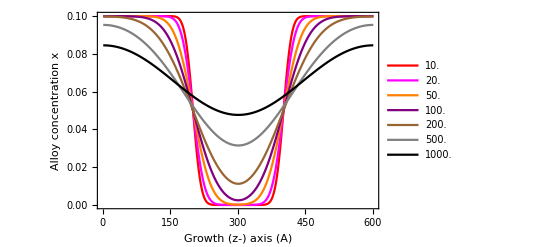

```mathematica
color={Red,Magenta,Orange,Purple,Brown,Gray,Black};
Show[
Plot[x0/2 Erfc[(u-well)/(2 √(diff*tplots⟦4⟧))]+x0/2 Erfc[-(u-(border+well))/(2 √(diff*tplots⟦4⟧))],{u,1,z⟦-1⟧},PlotStyle->Gray],
ListPlot[Table[{z⟦i⟧,xplots⟦4,i⟧},{i,1,lz,15*dz}],PlotStyle-> Black],
Frame-> True, FrameLabel-> {"Growth (z-) axis (A)","Alloy concentration x"}
]

Show[
Plot[x0/2 Erfc[(u-well)/(2 √(diff*tplots⟦{4,7}⟧))]+x0/2 Erfc[-(u-(border+well))/(2 √(diff*tplots⟦{4,7}⟧))],{u,1,z⟦-1⟧},PlotStyle->Gray],
ListPlot[Table[{z⟦i⟧,xplots⟦j,i⟧},{i,1,lz,15*dz},{j,4,7,3}],PlotStyle-> Black],
Frame-> True, FrameLabel-> {"Growth (z-) axis (A)","Alloy concentration x"}
]
nplots=0.*tplots;
Do[nplots⟦i⟧=ListLinePlot[xplots⟦i⟧,PlotStyle-> color⟦i⟧,Frame->True,FrameLabel-> {"Growth (z-) axis (A)","Alloy concentration x"}]
,{i,Length[xplots]}];
Legended[Show[nplots],LineLegend[color,tplots]]
```

## Change in ground state of well after diffusion

```mathematica
ClearAll["Global`*"]

t0=AbsoluteTime[];
dz=1;dt=0.01;tf=1000.;
well=200.;border=200.;
lw=Floor[well/dz];lb=Floor[well/dz];
z=Range[0.,2*border+well,dz];lz=Length[z];
x=xp=0.*z;
x0=0.1;diff=10;
xp⟦Range[lb]⟧=xp⟦-Range[lb]⟧=ConstantArray[x0,lb];
tplots={0.,10.,20.,50.,100.,200.,500.,1000.};
xplots=0.*tplots;
n=1;

hom=7.62559/0.067;(*ℏ^2/m^* for GaAs in eV A^2*)
energy=0*tplots;

Do[
If[t==tplots⟦n⟧,
v=0.67*1.247*xp;
c=-0.5*hom/dz^2;b=hom/dz^2+v;

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c};
Do[H⟦i,{i-1,i,i+1}⟧= {c,b⟦i⟧,c},{i,2,lz-1}];
energy⟦n⟧=Sort[Eigenvalues[H]]⟦1⟧;
n++];
Do[
x⟦j⟧=xp⟦j⟧+dt*diff*1/dz^2(xp⟦j+1⟧-2xp⟦j⟧+xp⟦j-1⟧);
,{j,2,lz-1}];
x⟦{1,-1}⟧=x⟦{2,-2}⟧;
xp=x;

,{t,0.,tf,dt}];
```

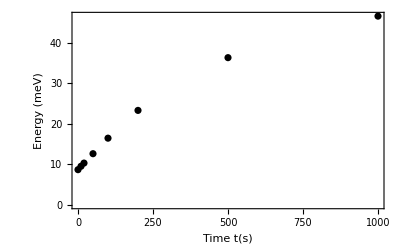

```mathematica
ListPlot[Table[{tplots⟦i⟧,1000*energy⟦i⟧},{i,Length[energy]}],Frame->True,FrameLabel->{"Time t(s)","Energy (meV)"},PlotStyle->Black]
```

## Diffusion in a δ-Doped Well

```mathematica
ClearAll["Global`*"]

t0=AbsoluteTime[];
dz=1;dt=0.01;tf=200.;
well=100.;border=50.;
lw=Floor[well/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well,dz];lz=Length[z];
x=xw=xp=0.*z;
x0=0.2;diff=1.;
xw⟦Range[lb]⟧=xw⟦-Range[lb]⟧=ConstantArray[x0,lb];
xp⟦lb+lw/2+1⟧=3.;

tplots={0.,20.,100.,200.};
xplots=0.*tplots;
n=1;


Do[
If[t==tplots⟦n⟧,
xplots⟦n⟧=xp;
n++];
Do[
x⟦j⟧=xp⟦j⟧+dt*diff*1/dz^2(xp⟦j+1⟧-2xp⟦j⟧+xp⟦j-1⟧);
,{j,2,lz-1}];
x⟦{1,-1}⟧=x⟦{2,-2}⟧;
xp=x;
,{t,0.,tf,dt}];
```

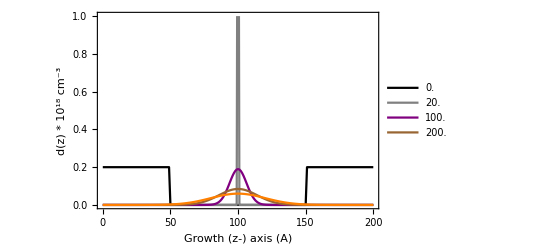

```mathematica
color={ Black,Gray, Purple,Brown,Orange };
plots={0,0,0,0,0};

Do[plots⟦i+1⟧=ListLinePlot[Table[{z⟦j⟧,xplots⟦i,j⟧},{j,lz}],
PlotRange->{0,1.},PlotStyle->color⟦i+1⟧],{i,1,Length[xplots]}]

plots⟦1⟧=ListLinePlot[Table[{z⟦i⟧,xw⟦i⟧},{i,1,lz}],PlotStyle->color⟦1⟧
,PlotRange->{0,1.0}];

Legended[
Show[plots,Frame->True,FrameLabel-> {"Growth (z-) axis (A)","d(z) * 10^18 cm^-3"}]
,LineLegend[color,tplots]
]
```

## Self Consistent Schrodinger-Poisson for Diffused δ-Doped Well

## Variable effective mass

```mathematica
ClearAll["Global`*"]
xmax=0.2;diff = 1.;
dt=0.01;tf=200.;
well=100.;barrierout=50.;
dz=1.;zmin=0.;zmax=2.*barrierout+well;
z=Range[zmin,zmax,dz];lz=Length[z];
lw=Floor[well/dz];lb=Floor[barrierout/dz];
xband=0.*z;(*Al concentration*)
xband⟦Range[lb]⟧=xband⟦-Range[lb]⟧=ConstantArray[xmax,lb];
vband=0.33*1.247xband;(*band-edge pontential eV*)
xd=xdp=0*z;(*donor concentration previous/current*)
ϵ=13.18*55.26349406*10^-4;(*e^2/(eV A)*)
tol = 0.000000001;

tplots = {0.,10.,20.,50.,100., 200.};
vplots=energy = 0*tplots;


xdp⟦lb+lw/2+1⟧=3.; (*donor concentration - previous*)
n=1;

Do[
If[t==tplots⟦n⟧,

σd=-xdp*10^-6;(*donor surface charge density e/A^2*)
charge = Abs[Total[σd]];(*total charge of the donors or the holes*)
v=vband;

m=(0.6+0.14xband);(*Heavy Hole mass*)
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;(*ℏ^2/(2 m^*) in eV A^2*)

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];

ψ= Eigenvectors[H]⟦-1⟧;
ep=Sort[Eigenvalues[H]]⟦-1⟧;
e=ep+tol+1.;

While[Abs[e-ep]>tol,
ep= e;
σh=charge*ψ^2*dz;
ef=vc=0.*z;
σ=σd+σh;
Do[ef⟦i⟧= (1/(2*ϵ))Sum[σ⟦j⟧*Sign[z⟦i⟧-z⟦j⟧],{j,lz}],{i,lz}];
Do[vc⟦i⟧=vc⟦i-1⟧-ef⟦i⟧*dz,{i,2,lz}];
v=vband+vc;
c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];

ψ=Eigenvectors[H]⟦-1⟧;
e=Sort[Eigenvalues[H]]⟦1⟧;
];
vplots⟦n⟧=vc;
energy⟦n⟧=e;
n++];

Do[
xd⟦j⟧=xdp⟦j⟧+dt*diff*1/dz^2(xdp⟦j+1⟧-2xdp⟦j⟧+xdp⟦j-1⟧);
,{j,2,lz-1}];
xd⟦{1,-1}⟧=xd⟦{2,-2}⟧;
xdp=xd;
,{t,0.,tf,dt}]
```

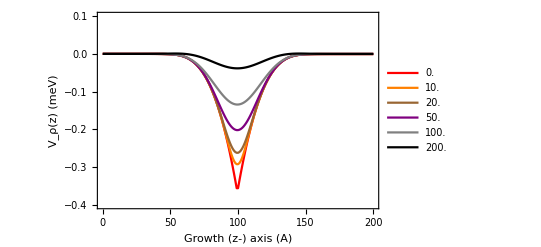

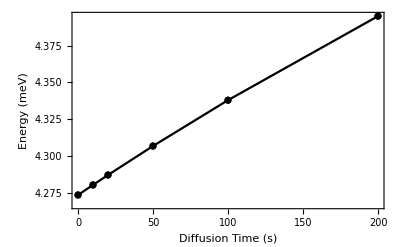

```mathematica
color={Red,Orange,Brown,Purple,Gray,Black};
plots=0*tplots;

Do[
plots⟦j⟧=ListLinePlot[Table[{z⟦i⟧,1000*vplots⟦j,i⟧},{i,lz}]
,PlotRange->{-0.4,0.1},PlotStyle->color⟦j⟧]
,{j,Length[vplots]}]

Legended[Show[plots,Frame->True,FrameLabel->{"Growth (z-) axis (A)","V_ρ(z) (meV)"}],LineLegend[color,tplots]]

ListPlot[Table[{tplots⟦i⟧,1000*energy⟦i⟧},{i,Length[tplots]}]
,PlotRange->All, PlotStyle->Black, Joined->True, Mesh->Full
,Frame->True,FrameLabel->{"Diffusion Time (s)","Energy (meV)"}]
```